```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
<<"HeterogeneousTemplate.wl";

GenerateMarkovTemplates[  MarkovProc_, NumTemplates_, LenTemplates_ ] :=
	(RandomFunction[MarkovProc,{#,LenTemplates}][[2]][[1]][[1]])&/@ConstantArray[1,NumTemplates];

RandomMarkovError[  Alphabet_,ProbVec_, LenTemplates_ ,gpo_,EnergyMatrix_,KineticMatrix_ ] :=  Module[ {inputtemplate,ErrorProbs},
	inputtemplate = RandomChoice[ ProbVec->Range[Alphabet],LenTemplates];
	ErrorProbs=(GetErrorProb[GetTransferMatrixList[gpo,
		EnergyMatrix,KineticMatrix,inputtemplate],inputtemplate]);
	Return[ErrorProbs];
 ]
```

```mathematica
gpo = 0.0;

PreDomain =  Range[0,1,0.05];
ErrorData= {};
Domain = {1-#,#} &/@PreDomain;

For [ x = 0.0,x<=6.1,x = x+1.0,
	EnergyMatrix =  {{6.0,x},{0,6.0}};
	KineticMatrix =  EnergyMatrix;
	Print[KineticMatrix];
	MeanErrors =RandomMarkovError[  2,#,100000,gpo,EnergyMatrix,KineticMatrix] &/@Domain;
	ErrorData =Append[ErrorData,Transpose@{PreDomain,MeanErrors}];
]
```

{{6.,0.},{0,6.}}

{{6.,1.},{0,6.}}

{{6.,2.},{0,6.}}

{{6.,3.},{0,6.}}

{{6.,4.},{0,6.}}

{{6.,5.},{0,6.}}

{{6.,6.},{0,6.}}

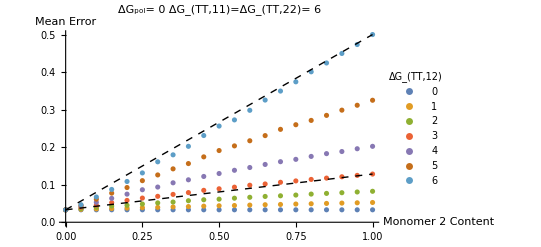

```mathematica
mu={0,1,2,3,4,5,6};
pl=PointLegend[mu,LegendLabel->Subscript["ΔG","TT,12"],LegendFunction->"Frame",LegendLayout->Automatic,LegendMarkers->Automatic];
p1 =ListPlot[ErrorData,AxesLabel->{"Monomer 2 Content","Mean Error"},
		PlotLegends->Placed[pl,Right],PlotLabel->Row[{Subscript["ΔG","pol"],"= 0    ", Subscript["ΔG","TT,11"],"=",
		Subscript["ΔG","TT,22"],"= 6    "}]];
p2 = Graphics[{Thick,Dashed,Line[{ErrorData[[7]][[1]],ErrorData[[7]][[-1]]}]}];
p3 = Graphics[{Thick,Dashed,Line[{ErrorData[[4]][[1]],ErrorData[[4]][[-1]]}]}];
Show[{p1,p2,p3}]
```

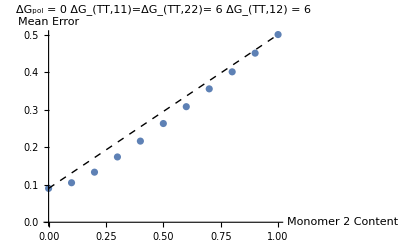

```mathematica
p1 =ListPlot[ErrorData[[7]],AxesLabel->{"Monomer 2 Content","Mean Error"}, 
	PlotLabel->Row[{Subscript["ΔG","pol"]," = 0    ",Subscript["ΔG","TT,11"],"=",
		Subscript["ΔG","TT,22"],"= 6    ", Subscript["ΔG","TT,12"], " = 6 "}]];
p2 = Graphics[{Thick,Dashed,Line[{ErrorData[[7]][[1]],ErrorData[[7]][[-1]]}]}];
Show[{p1,p2}]
```

0.1

{1,1,1,1,1,1,1,1,1,1,1,2,2,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1}

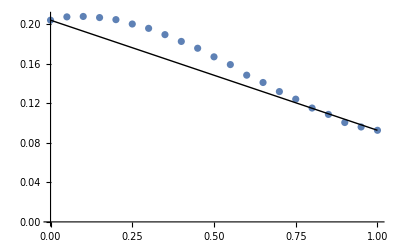

```mathematica
PreDomain[[3]]
RandomChoice[ {1-PreDomain[[3]],PreDomain[[3]]}->Range[2],100]
```

```mathematica
Save["CombIncorrect.Error",ErrorData]
```